# Arduino Tests

## Open the Device

Connect your Arduino UNO to the USB port and then check out the following line of code:

```mathematica
arduino=DeviceOpen["Arduino","COM60"]
```

```mathematica
Manipulate[
DeviceWrite[arduino,11->pwm/255],{pwm, 0, 255}
]
```

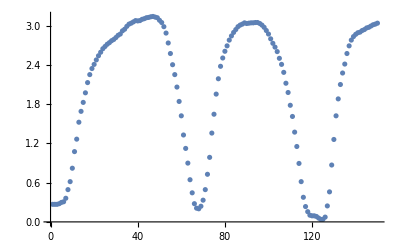

```mathematica
ListPlot[pressure = DeviceReadList[arduino, 150, "A5"]]
```

```mathematica
pF= ListInterpolation[QuantityMagnitude[pressure], {0, 3}]
```

InterpolatingFunction[…]

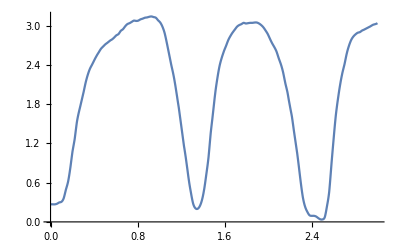

```mathematica
Plot[pF[t], {t, 0, 3}]
```

```mathematica
w = Table[Sin[pF[t]/3 *1000*t*2π], {t, 0, 3, 1/10000}];
```

```mathematica
MinMax[w]
```

{-1.,1.}

```mathematica
ListPlay[w, SampleRate->10000]
```

-Graphics-

```mathematica
DeviceClose[arduino]
```